# Simulating a system of repressors

## Introduction

In this relatively short programming assignment, you will write code to simulate a system of any number of interacting repressors. You will use the following model for the transcription rate of each mRNA:

S_i(p_1(…p)_n)=mSynth_i∏_(j=1)^n 1/(1+repStrength_(j,i)p_j)

This gets substituted in to the differential equation for the rate of change of concentration of each mRNA.

dm_i/dt=S_i(p_1(…p)_n)-mDeg_i*m_i

The concentrations of the proteins are governed by equations of the form

dp_i/dt=transRateC_i*m_i-pDeg_i*p_i

This produces a complex set of 2n coupled differential equations describing concentrations of the mRNA and protein products of n genes.

## Assignment

Your assignment is to write a function that will numerically integrate (i.e. simulate) these equations, starting from specified initial concentrations and going for a specified time. Shell code is provided in the accompanying .m file. The main task is to construct a list of 2n symbolic equations describing the rates of change of concentrations of the mRNA and protein products of n genes. Once you’ve constructed the equations the rest is just a matter of calling NDSolve, which is already there in the provided code.

### Inputs

The inputs to your function will be vectors and matrices of parameters for the equations.

A vector of length n specifying the unrepressed transcription rates of the n genes. In the equation above this is called mSynth_i .

An nxn matrix specifying the strength with which each protein represses each gene. In the equation above these parameters are called repStrength_(j,i). Each row (sublist) of the matrix (list) represents the repression strengths of one TF protein on all target genes.

A vector of length n specifying the mRNA degradation rates.

A vector of length n specifying the translation rates.

A vector of length n specifying the protein degradation rates.

A vector of length n specifying the initial mRNA concentrations (at time 0).

A vector of length n specifying the initial protein concentrations (at time 0).

The dimensions of these vectors and parameters will determine the number of genes n. Your code must work for any number of genes n.

### Outputs

The provided code prints out a graph of the concentrations versus time for times 0 to 10. You can change the final time if you need to. The graph won’t be readable for more than 2 genes but there’s no harm in printing it out.

After printing the graph, the code returns the result of a call to NDSolve on the system of equations you constructed.

Here is an example call.

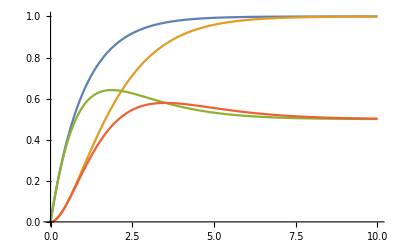

{{m[1]→InterpolatingFunction[{{0., 40.}}, <>],p[1]→InterpolatingFunction[{{0., 40.}}, <>],m[2]→InterpolatingFunction[{{0., 40.}}, <>],p[2]→InterpolatingFunction[{{0., 40.}}, <>]}}

```mathematica
nSolveRegVect[{1,1},{{0,1},{0,0}},{1,1},{1,1},{1,1},{0,0},{0,0}]
```

Note that this graph is identical to the one in the notebook repressorAndTarget, except possibly for the scale of the horizontal axis.

### Key tips and hints

#### Index the function names

For this lab, you must construct a set of symbolic equations whose length is determined by the input. This means you have to index the names of the functions somehow. Instead of using m1, m2, p1, p2 as function names,  use m[1], m[2], ...,p[1], p[2], .... Making the time dependence explicit gives us, for example, m[1][t], the derivative of which can be indicated by m[1]’[t]. So to programmatically construct a system of ODEs you can use, for example, Table[m[i]’[t]==...,{i, 1, n}], where the three dots indicates the right hand side of your equation.

#### Use Product

The equations you construct will each contain a product of up to n repression factors. To construct this product, use the built in function Product.

#### Use Flatten

The easiest way to do this is to construct all equations for a given gene at one time. There are four equations for each gene: rate of change of mRNA concentration, rate of change of protein concentration, mRNA concentration at time 0, and protein concentration at time 0. You may want to package these four equations into a sublist of the overall equation list. That’s fine -- just use Flatten at the end to make a single list of all equations.

#### Use the plot and inspect the equations

The test files are useful but, don’t rely only on the test files. The provided code outputs a plot of the concentrations versus time. This will probably be useful in debugging, but you can only see it when you run the code in a regular notebook -- it doesn’t show up when you run the test suite. Also, you will probably want to print out the list of equations you’ve constructed and handed to NDSolve, to make sure they look right.

## Grading

1 point for turning in something that runs and takes input and produces output of the right form. NDSolve must actually return a solution to whatever equations you generate. And you must generate some equations -- the empty list is not sufficient.

1 point for turning in code that generates the correct set of equations and gives the correct output.